```mathematica
ClearAll["Global`*"]
```

```mathematica
E2a[n_,k_, a_]:= E2a[n,k,a]=Sum[ E2a[n/j,k-1,a],{j,2,n}]-a Sum[ E2a[n/(a j),k-1,a],{j,1,n/a}];E2a[n_,0,a_]:=1
D2a[n_,k_]:=D2a[n,k]=Sum[D2a[Floor[n/j],k-1],{j,2,n}];D2a[n_,0]:=1
DD[n_,z_]:=DD[n,z]=Sum[FactorialPower[z,a]/a! D2a[n,a],{a,0,Log[2,n]}]
EE[n_,z_,b_]:=EE[n,z,b]=Sum[FactorialPower[z,a]/a! E2a[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
D1b[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1b[n/b^j,k,b],{j,0,Log[b,n]}]
D1b2[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1[n/b^j,k,b],{j,0,Log[b,n]}]
D1b2a[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1[n/b^j,k,b]/b,{j,0,Log[b,n]}]
E1b[n_,k_,b_]:=Sum[FactorialPower[k,a]/a! E2b[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
E2b[n_,k_, a_]:= E2b[n,k,a]=Sum[ E2b[n/j,k-1,a],{j,2,n}]-a Sum[ E2b[n/(a j),k-1,a],{j,1,n/a}];E2b[n_,0,a_]:=1
D1c[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
D1d[n_, z_, b_] := Sum[ 
Binomial[z+j-1,z-1]  Binomial[z,k]b^j  E2[n/b^j,k,b],{j,0,Log[b,n]},{k,0,Log[If[b>2,2,b],n/b^j]}]
D1e[n_, k_, b_] := Grid[Table[ 
Binomial[k+j-1,k-1]  Binomial[k,a]b^j  E2[n/b^j,a,b],{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1e2[n_, k_, b_] := Grid[Table[ 
Binomial[k+j-1,k-1]  FactorialPower[k,a]/a!b^j  E2[n/b^j,a,b]/k,{j,0,Log[b,n]},{a,0,Log[If[b>2,2,b],n/b^j]}]]
D1c2[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2b[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
lin[n_,b_]:=Sum[(-1)^(k+1)/k E2b[n,k,b],{k,1,Log[2,n]}]
M2[n_,a_]:=Sum[(-1)^k( E2b[n,k,a]-a E2b[n/a,k,a]),{k,0,Log[a,n]}]

EM2[n_,a_,b_] := EM2[n,a,b]=Sum[(-1)^k Binomial[k-1,k-a]E2a[n,k,b],{k,1,Log[If[b<2,b,2],n]}];EM2[n_,0,b_]:=1
E2d[n_,a_,b_] := E2d[n,a,b]=Sum[(-1)^k Binomial[k-1,k-a]EM2[n,k,b],{k,1,Log[If[b<2,b,2],n]}];E2d[n_,0,b_]:=1
E1e[n_,k_,b_]:=Sum[FactorialPower[k,a]/a! E2d[n,a,b],{a,0,Log[If[b>2,2,b],n]}]
D1g[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1e[n/b^j,k,b],{j,0,Log[b,n]}]

EP2[n_,a_,b_] := EP2[n,a,b]=Sum[SeriesCoefficient[Series[(Log[x+1])^a,{x,0,30}],k]E2a[n,k,b],{k,1,Log[If[b>2,2,b],n]}]
E1p[n_,a_,b_] := E1p[n,a,b]=1+Sum[a^k/k! EP2[n,k,b],{k,1,Log[If[b>2,2,b],n]}]
D1f[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j E1p[n/b^j,k,b],{j,0,Log[b,n]}]

E2d[100,4,1.5]
```

84.25

```mathematica
E2a[100,4,1.5]
```

84.25

```mathematica
D1g[300,-1,1.5]
```

-5.

```mathematica
D1c[300,-1,1.5]
```

-5.

```mathematica
E1p[300,3,1.5]
```

-48.

```mathematica
E1b[300,3,1.5]
```

-48.

```mathematica
D1f[300,-1,1.5]
```

-5.

```mathematica
D1e2[200,.0000001,2]
```

1.×10^7 E2[200,0,2] | 1. E2[200,1,2] | -0.5 E2[200,2,2] | 0.333333 E2[200,3,2] | -0.25 E2[200,4,2] | 0.2 E2[200,5,2] | -0.166667 E2[200,6,2] | 0.142857 E2[200,7,2]
2. E2[100,0,2] | 2.×10^-7 E2[100,1,2] | -1.×10^-7 E2[100,2,2] | 6.66667×10^-8 E2[100,3,2] | -5.×10^-8 E2[100,4,2] | 4.×10^-8 E2[100,5,2] | -3.33333×10^-8 E2[100,6,2] | 
2. E2[50,0,2] | 2.×10^-7 E2[50,1,2] | -1.×10^-7 E2[50,2,2] | 6.66667×10^-8 E2[50,3,2] | -5.×10^-8 E2[50,4,2] | 4.×10^-8 E2[50,5,2] |  | 
2.66667 E2[25,0,2] | 2.66667×10^-7 E2[25,1,2] | -1.33333×10^-7 E2[25,2,2] | 8.88889×10^-8 E2[25,3,2] | -6.66667×10^-8 E2[25,4,2] |  |  | 
4. E2[25/2,0,2] | 4.×10^-7 E2[25/2,1,2] | -2.×10^-7 E2[25/2,2,2] | 1.33333×10^-7 E2[25/2,3,2] |  |  |  | 
6.4 E2[25/4,0,2] | 6.4×10^-7 E2[25/4,1,2] | -3.2×10^-7 E2[25/4,2,2] |  |  |  |  | 
10.6667 E2[25/8,0,2] | 1.06667×10^-6 E2[25/8,1,2] |  |  |  |  |  | 
18.2857 E2[25/16,0,2] |  |  |  |  |  |  |

```mathematica
D1e[900,-1/2,2]
```

E2[900,0,2] | -1/2 E2[900,1,2] | 3/8 E2[900,2,2] | -5/16 E2[900,3,2] | 35/128 E2[900,4,2] | -63/256 E2[900,5,2] | (231 E2[900,6,2])/1024 | -(429 E2[900,7,2])/2048 | (6435 E2[900,8,2])/32768 | -(12155 E2[900,9,2])/65536
-E2[450,0,2] | 1/2 E2[450,1,2] | -3/8 E2[450,2,2] | 5/16 E2[450,3,2] | -35/128 E2[450,4,2] | 63/256 E2[450,5,2] | -(231 E2[450,6,2])/1024 | (429 E2[450,7,2])/2048 | -(6435 E2[450,8,2])/32768 | 
-1/2 E2[225,0,2] | 1/4 E2[225,1,2] | -3/16 E2[225,2,2] | 5/32 E2[225,3,2] | -35/256 E2[225,4,2] | 63/512 E2[225,5,2] | -(231 E2[225,6,2])/2048 | (429 E2[225,7,2])/4096 |  | 
-1/2 E2[225/2,0,2] | 1/4 E2[225/2,1,2] | -3/16 E2[225/2,2,2] | 5/32 E2[225/2,3,2] | -35/256 E2[225/2,4,2] | 63/512 E2[225/2,5,2] | -(231 E2[225/2,6,2])/2048 |  |  | 
-5/8 E2[225/4,0,2] | 5/16 E2[225/4,1,2] | -15/64 E2[225/4,2,2] | 25/128 E2[225/4,3,2] | -(175 E2[225/4,4,2])/1024 | (315 E2[225/4,5,2])/2048 |  |  |  | 
-7/8 E2[225/8,0,2] | 7/16 E2[225/8,1,2] | -21/64 E2[225/8,2,2] | 35/128 E2[225/8,3,2] | -(245 E2[225/8,4,2])/1024 |  |  |  |  | 
-21/16 E2[225/16,0,2] | 21/32 E2[225/16,1,2] | -63/128 E2[225/16,2,2] | 105/256 E2[225/16,3,2] |  |  |  |  |  | 
-33/16 E2[225/32,0,2] | 33/32 E2[225/32,1,2] | -99/128 E2[225/32,2,2] |  |  |  |  |  |  | 
-429/128 E2[225/64,0,2] | 429/256 E2[225/64,1,2] |  |  |  |  |  |  |  | 
-715/128 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,-1,2]
```

E2[900,0,2] | -E2[900,1,2] | E2[900,2,2] | -E2[900,3,2] | E2[900,4,2] | -E2[900,5,2] | E2[900,6,2] | -E2[900,7,2] | E2[900,8,2] | -E2[900,9,2]
-2 E2[450,0,2] | 2 E2[450,1,2] | -2 E2[450,2,2] | 2 E2[450,3,2] | -2 E2[450,4,2] | 2 E2[450,5,2] | -2 E2[450,6,2] | 2 E2[450,7,2] | -2 E2[450,8,2] | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,-2,2]
```

E2[900,0,2] | -2 E2[900,1,2] | 3 E2[900,2,2] | -4 E2[900,3,2] | 5 E2[900,4,2] | -6 E2[900,5,2] | 7 E2[900,6,2] | -8 E2[900,7,2] | 9 E2[900,8,2] | -10 E2[900,9,2]
-4 E2[450,0,2] | 8 E2[450,1,2] | -12 E2[450,2,2] | 16 E2[450,3,2] | -20 E2[450,4,2] | 24 E2[450,5,2] | -28 E2[450,6,2] | 32 E2[450,7,2] | -36 E2[450,8,2] | 
4 E2[225,0,2] | -8 E2[225,1,2] | 12 E2[225,2,2] | -16 E2[225,3,2] | 20 E2[225,4,2] | -24 E2[225,5,2] | 28 E2[225,6,2] | -32 E2[225,7,2] |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,-3,2]
```

E2[900,0,2] | -3 E2[900,1,2] | 6 E2[900,2,2] | -10 E2[900,3,2] | 15 E2[900,4,2] | -21 E2[900,5,2] | 28 E2[900,6,2] | -36 E2[900,7,2] | 45 E2[900,8,2] | -55 E2[900,9,2]
-6 E2[450,0,2] | 18 E2[450,1,2] | -36 E2[450,2,2] | 60 E2[450,3,2] | -90 E2[450,4,2] | 126 E2[450,5,2] | -168 E2[450,6,2] | 216 E2[450,7,2] | -270 E2[450,8,2] | 
12 E2[225,0,2] | -36 E2[225,1,2] | 72 E2[225,2,2] | -120 E2[225,3,2] | 180 E2[225,4,2] | -252 E2[225,5,2] | 336 E2[225,6,2] | -432 E2[225,7,2] |  | 
-8 E2[225/2,0,2] | 24 E2[225/2,1,2] | -48 E2[225/2,2,2] | 80 E2[225/2,3,2] | -120 E2[225/2,4,2] | 168 E2[225/2,5,2] | -224 E2[225/2,6,2] |  |  | 
0 | 0 | 0 | 0 | 0 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,-4,2]
```

E2[900,0,2] | -4 E2[900,1,2] | 10 E2[900,2,2] | -20 E2[900,3,2] | 35 E2[900,4,2] | -56 E2[900,5,2] | 84 E2[900,6,2] | -120 E2[900,7,2] | 165 E2[900,8,2] | -220 E2[900,9,2]
-8 E2[450,0,2] | 32 E2[450,1,2] | -80 E2[450,2,2] | 160 E2[450,3,2] | -280 E2[450,4,2] | 448 E2[450,5,2] | -672 E2[450,6,2] | 960 E2[450,7,2] | -1320 E2[450,8,2] | 
24 E2[225,0,2] | -96 E2[225,1,2] | 240 E2[225,2,2] | -480 E2[225,3,2] | 840 E2[225,4,2] | -1344 E2[225,5,2] | 2016 E2[225,6,2] | -2880 E2[225,7,2] |  | 
-32 E2[225/2,0,2] | 128 E2[225/2,1,2] | -320 E2[225/2,2,2] | 640 E2[225/2,3,2] | -1120 E2[225/2,4,2] | 1792 E2[225/2,5,2] | -2688 E2[225/2,6,2] |  |  | 
16 E2[225/4,0,2] | -64 E2[225/4,1,2] | 160 E2[225/4,2,2] | -320 E2[225/4,3,2] | 560 E2[225/4,4,2] | -896 E2[225/4,5,2] |  |  |  | 
0 | 0 | 0 | 0 | 0 |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  | 
0 | 0 | 0 |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  | 
0 |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,1/2,2]
```

E2[900,0,2] | 1/2 E2[900,1,2] | -1/8 E2[900,2,2] | 1/16 E2[900,3,2] | -5/128 E2[900,4,2] | 7/256 E2[900,5,2] | -(21 E2[900,6,2])/1024 | (33 E2[900,7,2])/2048 | -(429 E2[900,8,2])/32768 | (715 E2[900,9,2])/65536
E2[450,0,2] | 1/2 E2[450,1,2] | -1/8 E2[450,2,2] | 1/16 E2[450,3,2] | -5/128 E2[450,4,2] | 7/256 E2[450,5,2] | -(21 E2[450,6,2])/1024 | (33 E2[450,7,2])/2048 | -(429 E2[450,8,2])/32768 | 
3/2 E2[225,0,2] | 3/4 E2[225,1,2] | -3/16 E2[225,2,2] | 3/32 E2[225,3,2] | -15/256 E2[225,4,2] | 21/512 E2[225,5,2] | -(63 E2[225,6,2])/2048 | (99 E2[225,7,2])/4096 |  | 
5/2 E2[225/2,0,2] | 5/4 E2[225/2,1,2] | -5/16 E2[225/2,2,2] | 5/32 E2[225/2,3,2] | -25/256 E2[225/2,4,2] | 35/512 E2[225/2,5,2] | -(105 E2[225/2,6,2])/2048 |  |  | 
35/8 E2[225/4,0,2] | 35/16 E2[225/4,1,2] | -35/64 E2[225/4,2,2] | 35/128 E2[225/4,3,2] | -(175 E2[225/4,4,2])/1024 | (245 E2[225/4,5,2])/2048 |  |  |  | 
63/8 E2[225/8,0,2] | 63/16 E2[225/8,1,2] | -63/64 E2[225/8,2,2] | 63/128 E2[225/8,3,2] | -(315 E2[225/8,4,2])/1024 |  |  |  |  | 
231/16 E2[225/16,0,2] | 231/32 E2[225/16,1,2] | -231/128 E2[225/16,2,2] | 231/256 E2[225/16,3,2] |  |  |  |  |  | 
429/16 E2[225/32,0,2] | 429/32 E2[225/32,1,2] | -429/128 E2[225/32,2,2] |  |  |  |  |  |  | 
6435/128 E2[225/64,0,2] | 6435/256 E2[225/64,1,2] |  |  |  |  |  |  |  | 
12155/128 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,1,2]
```

E2[900,0,2] | E2[900,1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 E2[450,0,2] | 2 E2[450,1,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 
4 E2[225,0,2] | 4 E2[225,1,2] | 0 | 0 | 0 | 0 | 0 | 0 |  | 
8 E2[225/2,0,2] | 8 E2[225/2,1,2] | 0 | 0 | 0 | 0 | 0 |  |  | 
16 E2[225/4,0,2] | 16 E2[225/4,1,2] | 0 | 0 | 0 | 0 |  |  |  | 
32 E2[225/8,0,2] | 32 E2[225/8,1,2] | 0 | 0 | 0 |  |  |  |  | 
64 E2[225/16,0,2] | 64 E2[225/16,1,2] | 0 | 0 |  |  |  |  |  | 
128 E2[225/32,0,2] | 128 E2[225/32,1,2] | 0 |  |  |  |  |  |  | 
256 E2[225/64,0,2] | 256 E2[225/64,1,2] |  |  |  |  |  |  |  | 
512 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,2,2]
```

E2[900,0,2] | 2 E2[900,1,2] | E2[900,2,2] | 0 | 0 | 0 | 0 | 0 | 0 | 0
4 E2[450,0,2] | 8 E2[450,1,2] | 4 E2[450,2,2] | 0 | 0 | 0 | 0 | 0 | 0 | 
12 E2[225,0,2] | 24 E2[225,1,2] | 12 E2[225,2,2] | 0 | 0 | 0 | 0 | 0 |  | 
32 E2[225/2,0,2] | 64 E2[225/2,1,2] | 32 E2[225/2,2,2] | 0 | 0 | 0 | 0 |  |  | 
80 E2[225/4,0,2] | 160 E2[225/4,1,2] | 80 E2[225/4,2,2] | 0 | 0 | 0 |  |  |  | 
192 E2[225/8,0,2] | 384 E2[225/8,1,2] | 192 E2[225/8,2,2] | 0 | 0 |  |  |  |  | 
448 E2[225/16,0,2] | 896 E2[225/16,1,2] | 448 E2[225/16,2,2] | 0 |  |  |  |  |  | 
1024 E2[225/32,0,2] | 2048 E2[225/32,1,2] | 1024 E2[225/32,2,2] |  |  |  |  |  |  | 
2304 E2[225/64,0,2] | 4608 E2[225/64,1,2] |  |  |  |  |  |  |  | 
5120 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,4,2]
```

E2[900,0,2] | 4 E2[900,1,2] | 6 E2[900,2,2] | 4 E2[900,3,2] | E2[900,4,2] | 0 | 0 | 0 | 0 | 0
8 E2[450,0,2] | 32 E2[450,1,2] | 48 E2[450,2,2] | 32 E2[450,3,2] | 8 E2[450,4,2] | 0 | 0 | 0 | 0 | 
40 E2[225,0,2] | 160 E2[225,1,2] | 240 E2[225,2,2] | 160 E2[225,3,2] | 40 E2[225,4,2] | 0 | 0 | 0 |  | 
160 E2[225/2,0,2] | 640 E2[225/2,1,2] | 960 E2[225/2,2,2] | 640 E2[225/2,3,2] | 160 E2[225/2,4,2] | 0 | 0 |  |  | 
560 E2[225/4,0,2] | 2240 E2[225/4,1,2] | 3360 E2[225/4,2,2] | 2240 E2[225/4,3,2] | 560 E2[225/4,4,2] | 0 |  |  |  | 
1792 E2[225/8,0,2] | 7168 E2[225/8,1,2] | 10752 E2[225/8,2,2] | 7168 E2[225/8,3,2] | 1792 E2[225/8,4,2] |  |  |  |  | 
5376 E2[225/16,0,2] | 21504 E2[225/16,1,2] | 32256 E2[225/16,2,2] | 21504 E2[225/16,3,2] |  |  |  |  |  | 
15360 E2[225/32,0,2] | 61440 E2[225/32,1,2] | 92160 E2[225/32,2,2] |  |  |  |  |  |  | 
42240 E2[225/64,0,2] | 168960 E2[225/64,1,2] |  |  |  |  |  |  |  | 
112640 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
D1e[900,5,2]
```

E2[900,0,2] | 5 E2[900,1,2] | 10 E2[900,2,2] | 10 E2[900,3,2] | 5 E2[900,4,2] | E2[900,5,2] | 0 | 0 | 0 | 0
10 E2[450,0,2] | 50 E2[450,1,2] | 100 E2[450,2,2] | 100 E2[450,3,2] | 50 E2[450,4,2] | 10 E2[450,5,2] | 0 | 0 | 0 | 
60 E2[225,0,2] | 300 E2[225,1,2] | 600 E2[225,2,2] | 600 E2[225,3,2] | 300 E2[225,4,2] | 60 E2[225,5,2] | 0 | 0 |  | 
280 E2[225/2,0,2] | 1400 E2[225/2,1,2] | 2800 E2[225/2,2,2] | 2800 E2[225/2,3,2] | 1400 E2[225/2,4,2] | 280 E2[225/2,5,2] | 0 |  |  | 
1120 E2[225/4,0,2] | 5600 E2[225/4,1,2] | 11200 E2[225/4,2,2] | 11200 E2[225/4,3,2] | 5600 E2[225/4,4,2] | 1120 E2[225/4,5,2] |  |  |  | 
4032 E2[225/8,0,2] | 20160 E2[225/8,1,2] | 40320 E2[225/8,2,2] | 40320 E2[225/8,3,2] | 20160 E2[225/8,4,2] |  |  |  |  | 
13440 E2[225/16,0,2] | 67200 E2[225/16,1,2] | 134400 E2[225/16,2,2] | 134400 E2[225/16,3,2] |  |  |  |  |  | 
42240 E2[225/32,0,2] | 211200 E2[225/32,1,2] | 422400 E2[225/32,2,2] |  |  |  |  |  |  | 
126720 E2[225/64,0,2] | 633600 E2[225/64,1,2] |  |  |  |  |  |  |  | 
366080 E2[225/128,0,2] |  |  |  |  |  |  |  |  |

```mathematica
Residue[ (( Zeta[s])) x^s s^(-1),{s,1}]
```

x

```mathematica
Residue[ (( Zeta[s]^2)) x^s /s,{s,1}]
```

-x+2 EulerGamma x+x Log[x]

```mathematica
FullSimplify[Residue[ (( Zeta[s]^3)) x^s /s,{s,1}]]
```

1/2 x (2+6 (-1+EulerGamma) EulerGamma+Log[x] (-2+6 EulerGamma+Log[x])-6 StieltjesGamma[1])

```mathematica
FullSimplify[Residue[ (( Zeta[s]^4)) x^s /s,{s,1}]]
```

1/6 x (3 (-1+4 EulerGamma) Log[x]^2+Log[x]^3+6 Log[x] (1-4 EulerGamma+6 EulerGamma^2-4 StieltjesGamma[1])+6 (-1+2 EulerGamma (2+EulerGamma (-3+2 EulerGamma)-6 StieltjesGamma[1])+4 StieltjesGamma[1]+2 StieltjesGamma[2]))

```mathematica
Limit[ (a-1)^2 Sum[k a^k ,{k,1,Log[a,x]}],a->1]
```

1-x+x Log[x]

```mathematica
Residue[ (( Zeta[s]^2)) x^s /s,{s,1}]
```

-x+2 EulerGamma x+x Log[x]

```mathematica
D1e[100,2,2]
```

E2[100,0,2] | 2 E2[100,1,2] | E2[100,2,2] | 0 | 0 | 0 | 0
4 E2[50,0,2] | 8 E2[50,1,2] | 4 E2[50,2,2] | 0 | 0 | 0 | 
12 E2[25,0,2] | 24 E2[25,1,2] | 12 E2[25,2,2] | 0 | 0 |  | 
32 E2[25/2,0,2] | 64 E2[25/2,1,2] | 32 E2[25/2,2,2] | 0 |  |  | 
80 E2[25/4,0,2] | 160 E2[25/4,1,2] | 80 E2[25/4,2,2] |  |  |  | 
192 E2[25/8,0,2] | 384 E2[25/8,1,2] |  |  |  |  | 
448 E2[25/16,0,2] |  |  |  |  |  |

```mathematica
Series[(1/(x+1)-1)^1,{x,0,20}]
```

-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10-x^11+x^12-x^13+x^14-x^15+x^16-x^17+x^18-x^19+x^20+O[x]^21

```mathematica
Table[ (-1)^k Binomial[k-1,k-1]x^k,{k,1,20}]
```

{-x,x^2,-x^3,x^4,-x^5,x^6,-x^7,x^8,-x^9,x^10,-x^11,x^12,-x^13,x^14,-x^15,x^16,-x^17,x^18,-x^19,x^20}

```mathematica
Series[(1/(x+1)-1)^2,{x,0,20}]
```

x^2-2 x^3+3 x^4-4 x^5+5 x^6-6 x^7+7 x^8-8 x^9+9 x^10-10 x^11+11 x^12-12 x^13+13 x^14-14 x^15+15 x^16-16 x^17+17 x^18-18 x^19+19 x^20+O[x]^21

```mathematica
Table[ (-1)^k Binomial[k-1,k-2]x^k,{k,1,20}]
```

{0,x^2,-2 x^3,3 x^4,-4 x^5,5 x^6,-6 x^7,7 x^8,-8 x^9,9 x^10,-10 x^11,11 x^12,-12 x^13,13 x^14,-14 x^15,15 x^16,-16 x^17,17 x^18,-18 x^19,19 x^20}

```mathematica
Series[(1/(x+1)-1)^3,{x,0,20}]
```

-x^3+3 x^4-6 x^5+10 x^6-15 x^7+21 x^8-28 x^9+36 x^10-45 x^11+55 x^12-66 x^13+78 x^14-91 x^15+105 x^16-120 x^17+136 x^18-153 x^19+171 x^20+O[x]^21

```mathematica
Table[ (-1)^k Binomial[k-1,k-3]x^k,{k,1,20}]
```

{0,0,-x^3,3 x^4,-6 x^5,10 x^6,-15 x^7,21 x^8,-28 x^9,36 x^10,-45 x^11,55 x^12,-66 x^13,78 x^14,-91 x^15,105 x^16,-120 x^17,136 x^18,-153 x^19,171 x^20}

```mathematica
Series[(1/(x+1)-1)^4,{x,0,20}]
```

x^4-4 x^5+10 x^6-20 x^7+35 x^8-56 x^9+84 x^10-120 x^11+165 x^12-220 x^13+286 x^14-364 x^15+455 x^16-560 x^17+680 x^18-816 x^19+969 x^20+O[x]^21

```mathematica
Table[ (-1)^k Binomial[k-1,k-4]x^k,{k,1,20}]
```

{0,0,0,x^4,-4 x^5,10 x^6,-20 x^7,35 x^8,-56 x^9,84 x^10,-120 x^11,165 x^12,-220 x^13,286 x^14,-364 x^15,455 x^16,-560 x^17,680 x^18,-816 x^19,969 x^20}

```mathematica
M2[n_,a_] := Sum[(-1)^k Binomial[k-1,k-a]D2a[n,k],{k,1,Log[2,n]}]
```

```mathematica
M2[1000,4]
```

199

```mathematica
MM[n_,k_] := Sum[ MoebiusMu[j]MM[Floor[n/j],k-1],{j,2,n}];MM[n_,0]:=1
```

```mathematica
MM[1000,4]
```

199

```mathematica
EM2[n_,a_,b_] := EM2[n,a,b]=Sum[(-1)^k Binomial[k-1,k-a]E2a[n,k,b],{k,1,Log[If[b<2,b,2],n]}]
```

```mathematica
EM2[100,2,1.1]
```

108.295

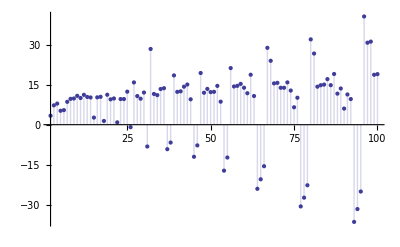

```mathematica
DiscretePlot[EM2[n,1,1.2],{n,2,100}]
```

```mathematica
Series[(Log[x+1])^(2),{x,0,20}]
```

x^2-x^3+(11 x^4)/12-(5 x^5)/6+(137 x^6)/180-(7 x^7)/10+(363 x^8)/560-(761 x^9)/1260+(7129 x^10)/12600-(671 x^11)/1260+(83711 x^12)/166320-(6617 x^13)/13860+(1145993 x^14)/2522520-(1171733 x^15)/2702700+(1195757 x^16)/2882880-(143327 x^17)/360360+(42142223 x^18)/110270160-(751279 x^19)/2042040+(275295799 x^20)/775975200+O[x]^21

```mathematica
SeriesCoefficient[Series[(Log[x+1])^2,{x,0,20}],4]
```

11/12

```mathematica
P2[n_,a_] := Sum[SeriesCoefficient[Series[(Log[x+1])^a,{x,0,30}],k]D2a[n,k],{k,1,Log[2,n]}]
```

```mathematica
P2[100,2]
```

16289/180

```mathematica
PP[n_,k_] := Sum[ (FullSimplify[MangoldtLambda[j]/Log[j]])PP[Floor[n/j],k-1],{j,2,n}];PP[n_,0]:=1
```

```mathematica
PP[100,2]
```

16289/180

```mathematica
EP2[n_,a_,b_] := EP2[n,a,b]=Sum[SeriesCoefficient[Series[(Log[x+1])^a,{x,0,30}],k]E2a[n,k,b],{k,1,Log[If[b>2,2,b],n]}]
```

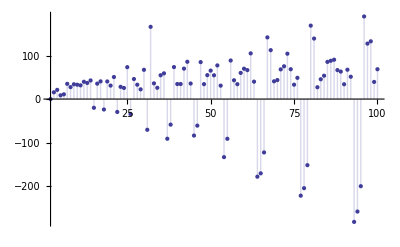

```mathematica
DiscretePlot[EP2[n,4,1.2],{n,2,100}]
```